```mathematica
Clear["Global`*"]
R=1;
r[s_,u_]:=HeavisideTheta[s-u]*R;
rb[u_]:=R(1-u);
Ι[k_,u_,t_]:=Integrate[(r[s,u]t)^k/Factorial[k] Exp[-r[s,u]t]*Log2[(r[s,u]^k Exp[-r[s,u]t])/(rb[u]^k Exp[-rb[u] t])],{s,0,1}];
Ι[k_,u_,t_]:=Integrate[(R t)^k/Factorial[k] Exp[-R t]*Log2[(R^k Exp[-R t])/(rb[u]^k Exp[-rb[u] t])],{s,u,1}]
p0[u_,t_]:=u+(1-u)Exp[-R t];
Ιk0[u_,t_]:=p0[u,t]Log2[Exp[rb[u] t]]+(p0[u,t]-u)Log2[Exp[-R t]];
```

```mathematica
FullSimplify[(R t)^k/Factorial[k] Exp[-R t]*Log2[(R^k Exp[-R t])/(rb[u]^k Exp[-rb[u] t])]]
```

(ⅇ^-t t^k Log[ⅇ^(-t u) (1-u)^-k])/(k! Log[2])

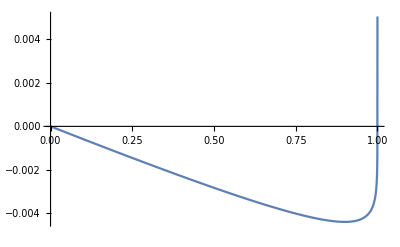

```mathematica
Plot[(R t)^k/Factorial[k] Exp[-R t]*Log2[(R^k Exp[-R t])/(rb[u]^k Exp[-rb[u] t])]/.{k->1,t->10},{u,0,1}]
```

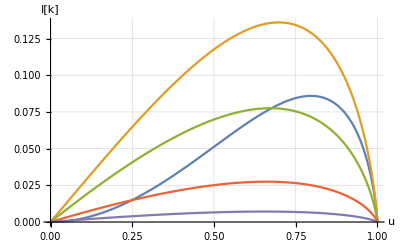

```mathematica
Plot[Evaluate@Table[Ι[k,u,1],{k,1,5}],{u,0,1},AxesLabel->{"u","I[k]"},PlotRange->Full,GridLines->Automatic]
```

```mathematica
umax[k_,t_]=Solve[D[Ι[k,u,t],u]==0,u][[1,1,2]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
p1=ListPlot[Table[{k,umax[k,0.1]},{k,1,1000,10}],AxesLabel->{"k","umax"},PlotLegends->{"t=0.1 (small)"},PlotRange->{{0,1000},{0,1.2}}];
p2=ListPlot[Table[{k,umax[k,100]},{k,1,1000,10}],AxesLabel->{"k","umax"},PlotStyle->{Red}, PlotLegends->{"t=100 (large)"}];
```

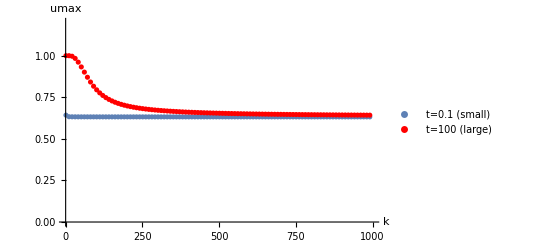

```mathematica
Show[p1,p2]
```

```mathematica
Limit[umax[k,100],{k->∞}]
```

(-1+ⅇ)/ⅇ

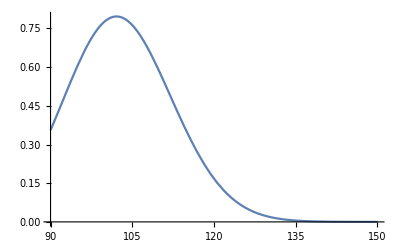

```mathematica
Plot[Ι[k,1-1/ⅇ,100],{k,90,150}]
```

```mathematica
R*100/(ⅇ Log[2])
```

100/(ⅇ Log[2])

```mathematica
N[100/(ⅇ Log[2])]
```

53.0738

```mathematica
Sum[Ι[k,1-1/ⅇ,1000000],{k,,1000}]//N
```

NSum::nslim: Limit of summation Null is not a number.

General::stop: Further output of NSum::nslim will be suppressed during this calculation.

NSum[(1000000^k Log[ⅇ^(-1000000+1000000/ⅇ+k)])/(ⅇ^1000001 k! Log[2]),{k,Null,1000}]

```mathematica
NIntegrate[Ι[k,1-1/ⅇ,100],{k,1,10}]
```

-1.27118×10^-29

```mathematica
Clear["Global`*"]
R=1;
r[s_]:=s*R;
rb=R/2;
Ιbinary[k_,u_,t_]:=Integrate[(R t)^k/Factorial[k] Exp[-R t]*Log2[(R^k Exp[-R t])/(R(1-u)^k Exp[-R(1-u) t])],{s,u,1}]
Ιlinear[k_,t_]:=NIntegrate[(r[s]t)^k/Factorial[k] Exp[-r[s]t]*Log2[(r[s]^k Exp[-r[s]t])/(rb^k Exp[-rb t])],{s,0,1}];
```

```mathematica
Ιbinary[1,1-1/ⅇ,0.01]//N
```

0.00522135

```mathematica
Ιlinear[1,0.01]//N
```

0.00136414

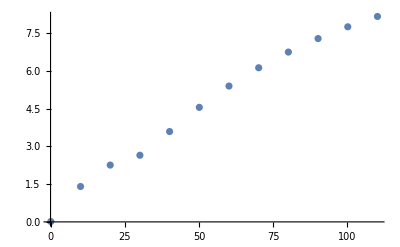

```mathematica
ListPlot[Table[{t,Sum[Ιlinear[k,t],{k,0,20}]},{t,0.1,120,10}]]
```

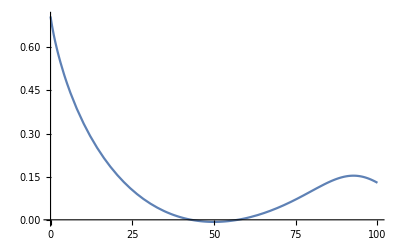

NIntegrate::inumr: The integrand (100^k ⅇ^(-100 s) s^k Log[2^k ⅇ^(50-100 s) s^k])/(k! Log[2]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

12.3263

```mathematica
Plot[Ιlinear[k,100],{k,0,100},PlotRange->Full]
```

```mathematica
Limit[(r[s]t)^k/Factorial[k] Exp[-r[s]t]*Log2[(r[s]^k Exp[-r[s]t])/(rb^k Exp[-rb t])],{t->∞}]
```

$Aborted

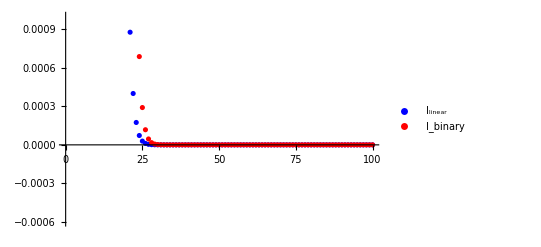

```mathematica
p1=ListPlot[Table[{k,Ιlinear[k,10]},{k,1,100}],PlotStyle->Blue,PlotLegends->{"I_linear"}];
p2=ListPlot[Table[{k,Ιbinary[k,1-1/ⅇ,10]},{k,1,100}],PlotStyle->Red,PlotLegends->{"I_binary"}];
Show[p1,p2]
```